```mathematica
ariasD[0] = 1;
ariasD[n_Integer?Positive] := ariasD[n] = Sum[2^((k (k - 1) - n (n - 1))/2) ariasD[k]/(n - k + 1)!, {k, 0, n - 1}]/(2^n - 1);
iFabiusF[x_]:=Module[{prec=Precision[x],n,p,q,s,tol,w,y,z},If[x<0,Return[0,Module]];tol=10^(-prec);
z=SetPrecision[x,Infinity];s=1;y=0;
z=If[0≤z≤2,1-Abs[1-z],q=Quotient[z,2];
If[ThueMorse[q]==1,s=-1];
1-Abs[1-z+2 q]];
While[z>0,n=-Floor[RealExponent[z,2]];p=2^n;
z-=1/p;w=1;
Do[w=ariasD[m]+p z w/(n-m+1);p/=2,{m,n}];
y=w-y;
If[Abs[w]<Abs[y] tol,Break[]]];
SetPrecision[s Abs[y],prec]];
FabiusF[Infinity] = Interval[{-1, 1}];
FabiusF[x_?NumberQ] /; If[Im[x] == 0, TrueQ[Composition[BitAnd[#, # - 1] &, Denominator][x] == 0], False] := iFabiusF[x];
Derivative[n_Integer][FabiusF] := 2^(n (n + 1)/2) FabiusF[2^n #] &;
SetAttributes[FabiusF, {NumericFunction, Listable}];//Timing//AbsoluteTiming
```

{0.0000134748,{0.,Null}}

```mathematica
ClearAll[iCurvaturePlotHelper, CurvaturePlot]
iCurvaturePlotHelper[f_?(Head[#] =!= List &), {t_, tmin_, tmax_}, {{x0_, y0_}, θ0_}, opts : OptionsPattern[]] := Module[{sol, θ, x, y, if},
  sol = NDSolve[{
     θ'[t] == f,
     x'[t] == Cos[θ[t]],
     y'[t] == Sin[θ[t]],
     θ[tmin] == θ0,
     x[tmin] == x0,
     y[tmin] == y0
     }, {x, y}, {t, tmin, tmax}, opts];
  if = {x[#], y[#]} & /. First[sol];
  if]
CurvaturePlot[f_, {t_, tmin_, tmax_}, opts : OptionsPattern[]] := CurvaturePlot[f, {t, tmin, tmax}, {{0, 0}, 0}, opts]
CurvaturePlot[f_, {t_, tmin_, tmax_}, p : {{x0_, y0_}, θ0_}, opts : OptionsPattern[]] := Module[{θ, x, y, sol, rlsplot, rlsndsolve, if, ifs},
  rlsplot = FilterRules[{opts}, Options[ParametricPlot]];rlsndsolve = FilterRules[{opts}, Options[NDSolve]];
  If[Head[f] === List,
   ifs = iCurvaturePlotHelper[#, {t, tmin, tmax}, p, Evaluate@(Sequence @@ rlsndsolve)] & /@ f;
   ParametricPlot[Evaluate[#[tplot] & /@ ifs], {tplot, tmin, tmax}, Evaluate@(Sequence @@ rlsplot)]
   ,
   if = iCurvaturePlotHelper[f, {t, tmin, tmax}, p, Evaluate@(Sequence @@ rlsndsolve)];
   ParametricPlot[Evaluate[if[tplot]], {tplot, tmin, tmax}, Evaluate@(Sequence @@ rlsplot)]
   ]];//Timing//AbsoluteTiming
```

{0.0000682926,{0.,Null}}

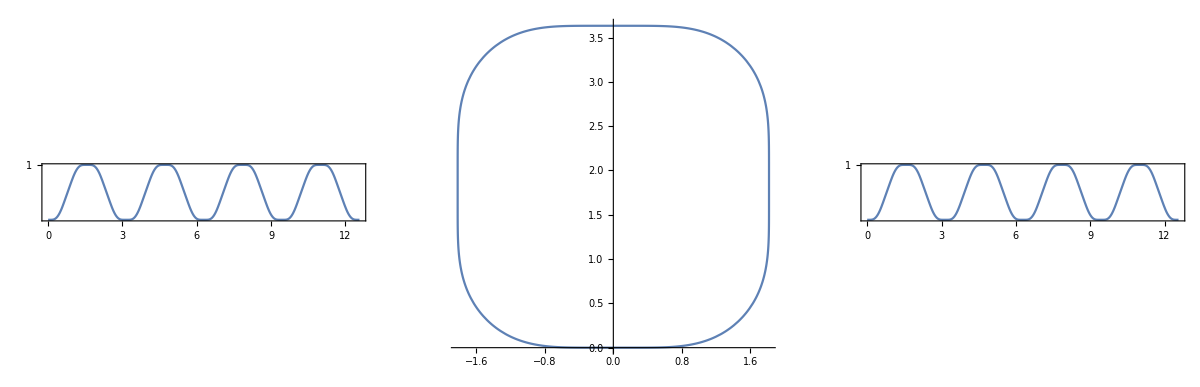

```mathematica
⚪ᔓᔕ⚪ᑎ⚪ꖴ⚪8⚪ᗩ⚪ꗳ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ꗳ⚪ᗩ⚪8⚪ꖴ⚪ᑎ⚪ᔓᔕ⚪ = Abs[FabiusF[X/π*2]];
GraphicsGrid[
{
{
Plot[⚪ᔓᔕ⚪ᑎ⚪ꖴ⚪8⚪ᗩ⚪ꗳ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ꗳ⚪ᗩ⚪8⚪ꖴ⚪ᑎ⚪ᔓᔕ⚪,{X,0,4π},Axes->True,AspectRatio->.5/π,Frame->True,FrameTicks->{Automatic,{1}},ImageSize->Full],
CurvaturePlot[⚪ᔓᔕ⚪ᑎ⚪ꖴ⚪8⚪ᗩ⚪ꗳ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ꗳ⚪ᗩ⚪8⚪ꖴ⚪ᑎ⚪ᔓᔕ⚪,{X,0,4 π}, Axes -> {False,True},ImageSize->Full],
Plot[⚪ᔓᔕ⚪ᑎ⚪ꖴ⚪8⚪ᗩ⚪ꗳ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ꗳ⚪ᗩ⚪8⚪ꖴ⚪ᑎ⚪ᔓᔕ⚪,{X,0,4 π},Axes->True,AspectRatio->.5/π,Frame->True,FrameTicks->{Automatic,{1}},ImageSize->Full]
}
},
ImageSize->Full
]
```

```mathematica
Plot3D[FabiusF[1-x]*FabiusF[1-y],{x,-1,1},{y,-1,1},ColorFunction->Function[{x,y,z},Glow[GrayLevel[z]]],PlotRange->All,Mesh->None,AspectRatio->1,Lighting->None,ViewPoint->{0,0,Infinity},ImageSize->Large,Boxed->False,Axes->False,PlotPoints->17,BoundaryStyle->None]
```

-Graphics3D-

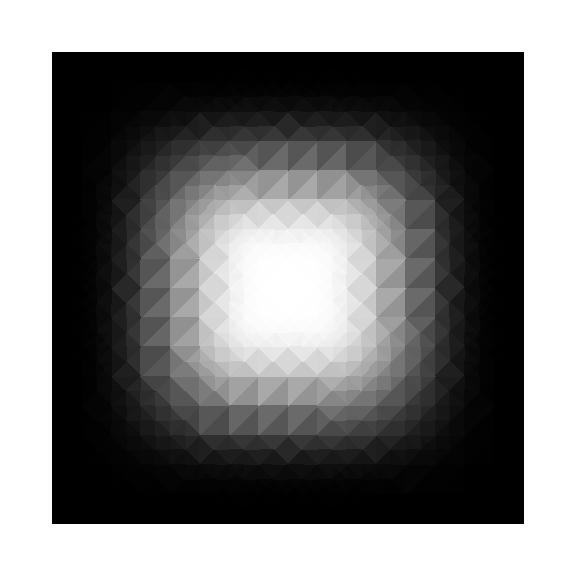

```mathematica
DensityPlot[FabiusF[1-x] FabiusF[1-y],{x,-1,1},{y,-1,1},ColorFunction->GrayLevel,Mesh->None,PlotPoints->17,ImageSize->Large,BoundaryStyle->None,Frame->None]
```

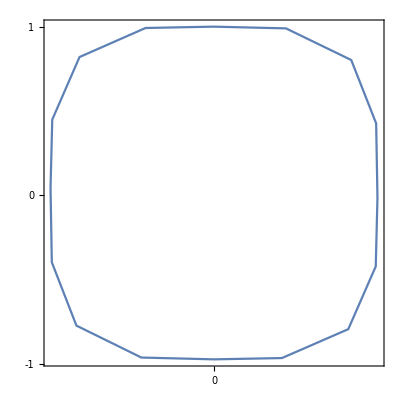

Show[{{6.479539127468569859047420322895050048828×10^-14,-0.9725678865241054182888547074981033802032},{0.1025032963763087556774422637317911721766,-0.964925481437592935662905802018940448761},{0.2025331942116540273612912415046594105661,-0.7936972931026409217025729958550073206425},{0.2439824412380121321231030151466256938875,-0.4217780747702383203900922126194927841425},{0.246570985811033788204227334972529206425,-0.01502072151155342538686454645358026027679},{0.2445968423752779841162663387876818887889,0.4263744817135346476533186432789079844952},{0.2070142275718628022129763621705933474004,0.8021893033527067728982729022391140460968},{0.108508803750153010048151713817787822336,0.9898175361441905462100976365036331117153},{-0.00103160254832607850561387863308482337743,1.},{-0.103234414084142231415874846334190806374,0.992076240790470853525562233699019998312},{-0.2028408743427731475428288376861019060016,0.8198859394114255128016566231963224709034},{-0.2439988990995674567052731163130374625325,0.4486529602662550075820035999640822410583},{-0.2465709858098660278713509796943981200457,0.0430801674432839121209326549433171749115},{-0.2446404222331298172754543429618934169412,-0.3971349872805177705359369610960129648447},{-0.2075156771658075438580226546037010848522,-0.772520676918624138451718863507267087698},{-0.1095496156993847336469372066858340986073,-0.9618898731136055202384227413858752697706},{5.324907181858407057006843388080596923828×10^-14,-0.9725678865243646553651046815502922981977}}]

```mathematica
⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪=CurvaturePlot[Evaluate[SetPrecision[SetAccuracy[⚪ᔓᔕ⚪ᑎ⚪ꖴ⚪8⚪ᗩ⚪ꗳ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ꗳ⚪ᗩ⚪8⚪ꖴ⚪ᑎ⚪ᔓᔕ⚪,Infinity],Infinity],{X,0,4π},WorkingPrecision->30,Accuracy->Infinity,MaxRecursion->0,PlotPoints->17], Axes -> {True,True}]/. {X_Real,Y_Real}:>{Evaluate[SetPrecision[SetAccuracy[Rescale[X,Last@PlotRange@⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪,{0,1}],40],40]],Evaluate[SetPrecision[SetAccuracy[Rescale[Y,Last@PlotRange@⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪,{-1,1}],40],40]]};
Show[⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪,Frame->True,FrameTicks->{{-1,0,1}, {-1,0,1}},PlotRange->Full,AspectRatio->1]/. {X_Real,Y_Real}:>{Evaluate[SetPrecision[SetAccuracy[Rescale[X,Last@PlotRange@⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪,{0,1}],40],40]],Evaluate[SetPrecision[SetAccuracy[Rescale[Y,Last@PlotRange@⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪,{-1,1}],40],40]]}
⚪ᗩ⚪✤⚪ᗩ⚪ᗝ⚪◯⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪◯⚪ᗝ⚪ᗩ⚪✤⚪ᗩ⚪=Flatten[Cases[⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪,Line[X__]->X,Infinity],1]/. {X_Real,Y_Real}:>{Evaluate[SetPrecision[SetAccuracy[Rescale[X,Last@PlotRange@⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪,{0,1}],40],40]],Evaluate[SetPrecision[SetAccuracy[Rescale[Y,Last@PlotRange@⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪,{-1,1}],40],40]]};
Export["⚪ᗩ⚪✤⚪ᗩ⚪ᗝ⚪◯⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪◯⚪ᗝ⚪ᗩ⚪✤⚪ᗩ⚪",⚪ᗩ⚪✤⚪ᗩ⚪ᗝ⚪◯⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪◯⚪ᗝ⚪ᗩ⚪✤⚪ᗩ⚪,"CSV"];
Show[⚪ᗩ⚪✤⚪ᗩ⚪ᗝ⚪◯⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪◯⚪ᗝ⚪ᗩ⚪✤⚪ᗩ⚪]
```